# Computing Covariance Functions From Power Spectral Representations

Bob Week
Feb 24, 2021

## Computing the Power Spectrum (ie, the Fourier Transform of the Cov fct)

Fourier transform of cov fct of 2d white noise

```mathematica
FourierTransform[ σ^2 DiracDelta[Subscript[x, 1]]DiracDelta[Subscript[x, 2]],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]
```

σ^2/(2 π)

Power spectrum and matrix thingy

```mathematica
ℋ={{Subscript[b, H](Subscript[κ, H]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2)),Subscript[b, HP]},{Subscript[b, PH],Subscript[b, P](Subscript[κ, P]^2+(Subscript[k, 1]^2+Subscript[k, 2]^2))}};
Subscript[S, V]={{Subscript[σ, H]^2,0},{0,Subscript[σ, P]^2}};
MatrixForm[ℋ]
MatrixForm[Subscript[S, V]]
```

(b_H (k_1^2+k_2^2+κ_H^2) | b_HP
b_PH | b_P (k_1^2+k_2^2+κ_P^2))

(σ_H^2 | 0
0 | σ_P^2)

```mathematica
Subscript[S, ζ]=Simplify[Inverse[ℋ].Subscript[S, V].Inverse[Transpose[ℋ]]];
MatrixForm[Subscript[S, ζ]]
```

((b_P^2 (k_1^2+k_2^2+κ_P^2)^2 σ_H^2+b_HP^2 σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2) (k_1^2+k_2^2+κ_P^2))^2) | -(b_P b_PH (k_1^2+k_2^2+κ_P^2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2) σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2) (k_1^2+k_2^2+κ_P^2))^2)
-(b_P b_PH (k_1^2+k_2^2+κ_P^2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2) σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2) (k_1^2+k_2^2+κ_P^2))^2) | (b_PH^2 σ_H^2+b_H^2 (k_1^2+k_2^2+κ_H^2)^2 σ_P^2)/((b_HP b_PH-b_H b_P (k_1^2+k_2^2+κ_H^2) (k_1^2+k_2^2+κ_P^2))^2))

Weak coupling approximation

```mathematica
Subscript[Ŝ, ζ]=Subscript[S, ζ]/.{Subscript[b, HP]^2->0,Subscript[b, PH]^2->0,Subscript[b, HP] Subscript[b, PH]->0};
Subscript[Ŝ, ζ]//MatrixForm
```

(σ_H^2/(2 π b_H^2 (k_1^2+k_2^2+κ_H^2)^2) | -(b_P b_PH (k_1^2+k_2^2+κ_P^2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2) σ_P^2)/(2 π b_H^2 b_P^2 (k_1^2+k_2^2+κ_H^2)^2 (k_1^2+k_2^2+κ_P^2)^2)
-(b_P b_PH (k_1^2+k_2^2+κ_P^2) σ_H^2+b_H b_HP (k_1^2+k_2^2+κ_H^2) σ_P^2)/(2 π b_H^2 b_P^2 (k_1^2+k_2^2+κ_H^2)^2 (k_1^2+k_2^2+κ_P^2)^2) | σ_P^2/(2 π b_P^2 (k_1^2+k_2^2+κ_P^2)^2))

```mathematica
Integrate[Subscript[Ŝ, ζ][[1,1]],{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞},Assumptions->Subscript[κ, H]^2>0]
```

σ_H^2/(2 b_H^2 κ_H^2)

```mathematica
Integrate[Subscript[Ŝ, ζ][[1,2]]/.{Subscript[α, H]->2,Subscript[α, P]->2},{Subscript[k, 1],-∞,+∞},{Subscript[k, 2],-∞,+∞},Assumptions->{Subscript[κ, H]^2>0,Subscript[κ, P]^2>0,Subscript[κ, H]≠0,Subscript[κ, P]}]
```

```mathematica
Subscript[Ĉ, HP,0]=Apart[-1/(Subscript[b, H]^2 Subscript[b, P]^2 Subscript[κ, H]^2 Subscript[κ, P]^2 (Subscript[κ, H]^2-Subscript[κ, P]^2)^2)(Subscript[b, P] Subscript[b, PH] Subscript[κ, P]^2 ((-1+Log[Subscript[κ, H]^2]-Log[Subscript[κ, P]^2]) Subscript[κ, H]^2+Subscript[κ, P]^2) Subscript[σ, H]^2+Subscript[b, H] Subscript[b, HP] Subscript[κ, H]^2 (Subscript[κ, H]^2+(-1-Log[Subscript[κ, H]^2]+Log[Subscript[κ, P]^2]) Subscript[κ, P]^2) Subscript[σ, P]^2)]
```

-(b_PH (-κ_H^2+Log[κ_H^2] κ_H^2-Log[κ_P^2] κ_H^2+κ_P^2) σ_H^2)/(b_H^2 b_P κ_H^2 (κ_H-κ_P)^2 (κ_H+κ_P)^2)-(b_HP (κ_H^2-κ_P^2-Log[κ_H^2] κ_P^2+Log[κ_P^2] κ_P^2) σ_P^2)/(b_H b_P^2 (κ_H-κ_P)^2 κ_P^2 (κ_H+κ_P)^2)

```mathematica
Subscript[Ŝ, ζ,12,0]=Subscript[Ŝ, ζ][[1,2]]/.{Subscript[α, H]->2,Subscript[α, P]->2,Subscript[k, 1]->0,Subscript[k, 2]->0}
```

-(b_P b_PH κ_P^2 σ_H^2+b_H b_HP κ_H^2 σ_P^2)/(b_H^2 b_P^2 κ_H^4 κ_P^4)

```mathematica
InverseFourierTransform[(Subscript[b, P]^2 (Subscript[k, 1]^2+Subscript[k, 2]^2+Subscript[κ, P]^2)^2 Subscript[σ, H]^2+Subscript[b, HP]^2 Subscript[σ, P]^2)/((Subscript[b, HP] Subscript[b, PH]-Subscript[b, H] Subscript[b, P] (Subscript[k, 1]^2+Subscript[k, 2]^2+Subscript[κ, H]^2) (Subscript[k, 1]^2+Subscript[k, 2]^2+Subscript[κ, P]^2))^2),{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 1],Subscript[x, 2]}]
```

#### Computing Integral Range of Interspecific Trait Covariance

```mathematica
Subscript[l, HP2]=FullSimplify[Subscript[Ŝ, ζ,12,0]/Subscript[Ĉ, HP,0]]
```

((κ_H^2-κ_P^2)^2 (b_P b_PH κ_P^2 σ_H^2+b_H b_HP κ_H^2 σ_P^2))/(b_P b_PH κ_H^2 κ_P^4 ((-1+Log[κ_H^2]-Log[κ_P^2]) κ_H^2+κ_P^2) σ_H^2+b_H b_HP κ_H^4 κ_P^2 (κ_H^2+(-1-Log[κ_H^2]+Log[κ_P^2]) κ_P^2) σ_P^2)

```mathematica
Subscript[l, HP2,C]=FullSimplify[FullSimplify[ExpandAll[Subscript[l, HP2]/.subs/.{Subscript[B, H]->ϵ Subscript[B, H],Subscript[B, P]->ϵ Subscript[B, P]}]/.{ϵ^2->0}]/.{ϵ^2->0,ϵ^3->0}/.{ϵ->1}]
```

ReplaceAll::reps: {subs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

((κ_H^2-κ_P^2)^2 (b_P b_PH κ_P^2 σ_H^2+b_H b_HP κ_H^2 σ_P^2))/(b_P b_PH κ_H^2 κ_P^4 ((-1+Log[κ_H^2]-Log[κ_P^2]) κ_H^2+κ_P^2) σ_H^2+b_H b_HP κ_H^4 κ_P^2 (κ_H^2+(-1-Log[κ_H^2]+Log[κ_P^2]) κ_P^2) σ_P^2)/.subs

#### Matern Covariance Function

```mathematica
M[x_,y_,ξ_,σ_,ν_]:=σ^2 2^(1-ν)/Gamma[ν](√(2ν)√(x^2+y^2)/ξ)^ν BesselK[ν,√(2ν)√(x^2+y^2)/ξ];
```

```mathematica
Mh[h_,ξ_,σ_,ν_]:=σ^2 2^(1-ν)/Gamma[ν](√(2ν)h/ξ)^ν BesselK[ν,√(2ν)h/ξ];
```

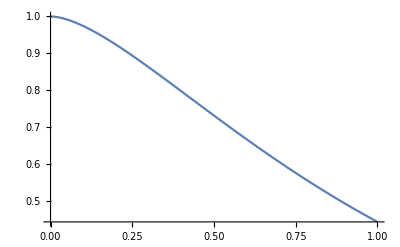

```mathematica
Plot[Mh[h,1,1,1],{h,0,1}]
```

```mathematica
Gamma[2]
```

1

## Coevolutionary Parameters

```mathematica
Element[Subscript[d, H],Reals];
Element[Subscript[G, H],Reals];
Element[Subscript[B, H],Reals];
Element[Subscript[A, H],Reals];
Element[Subscript[n, H],Reals];
Element[Subscript[d, P],Reals];
Element[Subscript[G, P],Reals];
Element[Subscript[B, P],Reals];
Element[Subscript[A, P],Reals];
Element[Subscript[n, P],Reals];
```

```mathematica
subs={Subscript[σ, H]-> √(Subscript[G, H]/Subscript[n, H]),Subscript[σ, P]-> √(Subscript[G, P]/Subscript[n, P]),Subscript[κ, H]->√((Subscript[G, H](Subscript[A, H]-Subscript[B, H]))/(Subscript[d, H]/2)),Subscript[κ, P]->√((Subscript[G, P](Subscript[A, P]+Subscript[B, P]))/(Subscript[d, P]/2)),Subscript[b, H]->Subscript[d, H]/2,Subscript[b, P]->Subscript[d, P]/2,Subscript[b, HP]->Subscript[G, H] Subscript[B, H],Subscript[b, PH]->-Subscript[G, P] Subscript[B, P]}
```

{σ_H→√(G_H/n_H),σ_P→√(G_P/n_P),κ_H→√2 √(((A_H-B_H) G_H)/d_H),κ_P→√2 √(((A_P+B_P) G_P)/d_P),b_H→d_H/2,b_P→d_P/2,b_HP→B_H G_H,b_PH→-B_P G_P}

```mathematica
MatrixForm[Subscript[S, ζ]/.subs]
```

(((d_P^2 G_H ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2)^2)/(4 n_H)+(B_H^2 G_H^2 G_P)/n_P)/(2 π (-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2) | -(-(B_P d_P G_H G_P ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))/(2 n_H)+(B_H d_H G_H G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2))/(2 n_P))/(2 π (-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2)
-(-(B_P d_P G_H G_P ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))/(2 n_H)+(B_H d_H G_H G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2))/(2 n_P))/(2 π (-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2) | ((B_P^2 G_H G_P^2)/n_H+(d_H^2 G_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2)^2)/(4 n_P))/(2 π (-B_H B_P G_H G_P-1/4 d_H d_P ((2 (A_H-B_H) G_H)/d_H+k_1^2+k_2^2) ((2 (A_P+B_P) G_P)/d_P+k_1^2+k_2^2))^2))

## Use Weak Selection Approximation

First try just weak biotic selection (B_H B_P,B_H^2,B_P^2~0)

```mathematica
Subscript[S, ζS]=FullSimplify[Subscript[S, ζ]/.subs/.{Subscript[B, H]->ϵ Subscript[B, H],Subscript[B, P]->ϵ Subscript[B, P]}/.{ϵ^2-> 0,ϵ^3->0,ϵ^4->0}/.{ϵ->1}];
MatrixForm[Subscript[S, ζS]]
```

((2 G_H)/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 n_H) | (4 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P)
(4 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P) | (2 G_P)/(π (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P))

```mathematica
Now try using the weakly coupled approximation
```

```mathematica
Subscript[Ŝ, ζS]=FullSimplify[Subscript[Ŝ, ζ]/.subs];
Subscript[Ŝ, ζS]//MatrixForm
```

((2 G_H)/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 n_H) | (4 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P)
(4 G_H G_P (-B_H (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) n_H+B_P (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_P))/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_H n_P) | (2 G_P)/(π (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P))

```mathematica
They're exactly the same
```

Splitting up that cross-cov term

```mathematica
(4 Subscript[G, H] Subscript[G, P] (Subscript[B, P] (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, P]))/(π (2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

(4 B_P G_H G_P)/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_H)

```mathematica
FullSimplify[Expand[(2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2)) ]/.{Subscript[B, H] Subscript[B, P]->0,Subscript[B, H]^2->0,Subscript[B, P]^2->0}]
```

(2 A_H G_H+d_H (k_1^2+k_2^2)) (2 A_P G_P (-4 B_H G_H+d_H (k_1^2+k_2^2))+2 A_H G_H (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))+(k_1^2+k_2^2) (2 B_P d_H G_P+d_P (-4 B_H G_H+d_H (k_1^2+k_2^2))))

```mathematica
(4 Subscript[G, H] Subscript[G, P] (-Subscript[B, H] (2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, H]))/(π (2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

-(4 B_H G_H G_P)/(π (2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

The marginals are easy (Matern functions with smoothness par = 1)

```mathematica
FullSimplify[FourierTransform[M[Subscript[x, 1],Subscript[x, 2],ξ,σ,1],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{ ξ->√(Subscript[d, H]/(Subscript[G, H](Subscript[A, H]-Subscript[B, H]))),σ^2->1/(Subscript[n, H] Subscript[d, H](Subscript[A, H]-Subscript[B, H])) }]
```

$Aborted

```mathematica
FourierTransform[M[Subscript[x, 1],Subscript[x, 2],√(Subscript[d, H]/((Subscript[A, H]-Subscript[B, H]) Subscript[G, H])),σ,1],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]
```

$Aborted

```mathematica
M[Subscript[x, 1],Subscript[x, 2],ξ,σ,1]/.{ξ->√(Subscript[d, H]/(Subscript[G, H](Subscript[A, H]-Subscript[B, H]))),σ^2->1/(Subscript[n, H] Subscript[d, H](Subscript[A, H]-Subscript[B, H])) }
```

(√2 BesselK[1,√2 √(((A_H-B_H) G_H)/d_H) √(x_1^2+x_2^2)] √(((A_H-B_H) G_H)/d_H) √(x_1^2+x_2^2))/((A_H-B_H) d_H n_H)

```mathematica
FullSimplify[1/(Subscript[n, P] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))FourierTransform[M[Subscript[x, 1],Subscript[x, 2],κ,1],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{κ->√((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

(4 G_P)/((2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

```mathematica
Subscript[C, 11]=FullSimplify[1/(Subscript[n, H] Subscript[d, H](Subscript[A, H]-Subscript[B, H]))M[Subscript[x, 1],Subscript[x, 2],κ,1]/.{κ->√((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H]))}];
Subscript[C, 22]=FullSimplify[1/(Subscript[n, P] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))M[Subscript[x, 1],Subscript[x, 2],κ,1]/.{κ->√((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}];
```

From this we see the marginal variances decrease with effective sizes, dispersal, and strengths of selection

Now let’s dive into the transformed cross-covariances...

```mathematica
Subscript[S, ζ12,1]=(8 Subscript[G, H] Subscript[G, P] (-Subscript[B, H] (2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, H]))/((2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

-(8 B_H G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2)) (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2))^2 n_P)

```mathematica
Subscript[S, ζ12,2]=(8 Subscript[G, H] Subscript[G, P] (Subscript[B, P] (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2)) Subscript[n, P]))/((2 (Subscript[A, H]-Subscript[B, H]) Subscript[G, H]+Subscript[d, H] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 (2 (Subscript[A, P]+Subscript[B, P]) Subscript[G, P]+Subscript[d, P] (Subscript[k, 1]^2+Subscript[k, 2]^2))^2 Subscript[n, H] Subscript[n, P])
```

(8 B_P G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_H)

These (^) are looking a lot like the F-transforms of convolutions of K_0 and Matern smooth-1 functions...

```mathematica
FullSimplify[(2 Subscript[G, H] Subscript[B, H])/(Subscript[n, P] Subscript[d, H] Subscript[d, P](Subscript[A, P]+Subscript[B, P]))FourierTransform[BesselK[0,Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]*FourierTransform[Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)BesselK[1,Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[κ, 1]-> √((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H])),Subscript[κ, 2]-> √((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

$Aborted

```mathematica
FullSimplify[(2 Subscript[G, P] Subscript[B, P])/(Subscript[n, H] Subscript[d, H] Subscript[d, P](Subscript[A, H]-Subscript[B, H]))FourierTransform[BesselK[0,Subscript[κ, 2] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]*FourierTransform[Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)BesselK[1,Subscript[κ, 1] √(Subscript[x, 1]^2+Subscript[x, 2]^2)],{Subscript[x, 1],Subscript[x, 2]},{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[κ, 1]-> √((2 Subscript[G, H])/Subscript[d, H](Subscript[A, H]-Subscript[B, H])),Subscript[κ, 2]-> √((2 Subscript[G, P])/Subscript[d, P](Subscript[A, P]+Subscript[B, P]))}]
```

(8 B_P G_H G_P)/((2 (A_H-B_H) G_H+d_H (k_1^2+k_2^2))^2 (2 (A_P+B_P) G_P+d_P (k_1^2+k_2^2)) n_H)

#### Correlation radii

```mathematica
Subscript[S, ζS0,11]=Subscript[S, ζS][[1,1]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0}
Subscript[S, ζS0,22]=Subscript[S, ζS][[2,2]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0}
```

1/((A_H-B_H)^2 G_H n_H)

1/((A_P+B_P)^2 G_P n_P)

```mathematica
FullSimplify[-(Laplacian[Subscript[S, ζS][[1,1]],{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[k, 1]->0,Subscript[k, 2]->0})/Subscript[S, ζS0,11]]
```

(4 d_H)/((A_H-B_H) G_H)

```mathematica
FullSimplify[-(Laplacian[Subscript[S, ζS][[2,2]],{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[k, 1]->0,Subscript[k, 2]->0})/Subscript[S, ζS0,22]]
```

(4 d_P)/((A_P+B_P) G_P)

```mathematica
Subscript[S, ζS0,12]=Subscript[S, ζS][[1,2]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0}
```

(-2 (A_H-B_H) B_H G_H n_H+2 B_P (A_P+B_P) G_P n_P)/(2 (A_H-B_H)^2 (A_P+B_P)^2 G_H G_P n_H n_P)

```mathematica
FullSimplify[-(Laplacian[Subscript[S, ζS][[1,2]],{Subscript[k, 1],Subscript[k, 2]}]/.{Subscript[k, 1]->0,Subscript[k, 2]->0})/Subscript[S, ζS0,12]]
```

(2 (A_H-B_H) B_H G_H (2 (A_H-B_H) d_P G_H+(A_P+B_P) d_H G_P) n_H-2 B_P (A_P+B_P) G_P ((A_H-B_H) d_P G_H+2 (A_P+B_P) d_H G_P) n_P)/((A_H-B_H) (A_P+B_P) G_H G_P ((A_H-B_H) B_H G_H n_H-B_P (A_P+B_P) G_P n_P))

```mathematica
Expand[(Subscript[A, H]-Subscript[B, H]) (Subscript[A, P]+Subscript[B, P]) Subscript[G, H] Subscript[G, P] ((Subscript[A, H]-Subscript[B, H]) Subscript[B, H] Subscript[G, H] Subscript[n, H]-Subscript[B, P] (Subscript[A, P]+Subscript[B, P]) Subscript[G, P] Subscript[n, P])]
```

A_H^2 A_P B_H G_H^2 G_P n_H-2 A_H A_P B_H^2 G_H^2 G_P n_H+A_P B_H^3 G_H^2 G_P n_H+A_H^2 B_H B_P G_H^2 G_P n_H-2 A_H B_H^2 B_P G_H^2 G_P n_H+B_H^3 B_P G_H^2 G_P n_H-A_H A_P^2 B_P G_H G_P^2 n_P+A_P^2 B_H B_P G_H G_P^2 n_P-2 A_H A_P B_P^2 G_H G_P^2 n_P+2 A_P B_H B_P^2 G_H G_P^2 n_P-A_H B_P^3 G_H G_P^2 n_P+B_H B_P^3 G_H G_P^2 n_P

## Integral Lengths

```mathematica
M1 = Subscript[κ, 1] √(Subscript[y, 1]^2+Subscript[y, 2]^2)BesselK[1,Subscript[κ, 1] √(Subscript[y, 1]^2+Subscript[y, 2]^2)]
M2 = BesselK[0,Subscript[κ, 2] √(Subscript[y, 1]^2+Subscript[y, 2]^2)]
```

BesselK[1,√(y_1^2+y_2^2) κ_1] √(y_1^2+y_2^2) κ_1

BesselK[0,√(y_1^2+y_2^2) κ_2]

```mathematica
Integrate[M1,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(4 π)/κ_1^2, κ_1>0]

```mathematica
Integrate[M1/.{√(Subscript[y, 1]^2+Subscript[y, 2]^2)->x},{x,0,∞}]
```

ConditionalExpression[π/(2 κ_1), κ_1>0]

```mathematica
Integrate[M2,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(2 π)/κ_2^2, κ_2>0]

```mathematica
Integrate[M2/.{√(Subscript[y, 1]^2+Subscript[y, 2]^2)->x},{x,0,∞}]
```

ConditionalExpression[π/(2 κ_2), κ_2>0]

```mathematica
Integrate[M1*M2,{Subscript[y, 1],-∞,∞},{Subscript[y, 2],-∞,∞}]
```

ConditionalExpression[(2 π ((-1+2 Log[κ_1]-2 Log[κ_2]) κ_1^2+κ_2^2))/((κ_1^2-κ_2^2)^2), κ_1>0&&κ_2>0]

```mathematica
Subscript[S, ζS][[1,2]]/.{Subscript[k, 1]->0,Subscript[k, 2]->0}
```

(-2 (A_H-B_H) B_H G_H n_H+2 B_P (A_P+B_P) G_P n_P)/(2 (A_H-B_H)^2 (A_P+B_P)^2 G_H G_P n_H n_P)

## Fitness differences

```mathematica
DiversitySubs={(Subscript[z, H][x])^2->Subscript[σ, H]^2+(Subscript[Z̄, H][x])^2,(Subscript[z, P][y])^2->Subscript[σ, P]^2+(Subscript[Z̄, P][y])^2,Subscript[z, H][x]Subscript[z, P][y]->Subscript[Z̄, H][x]Subscript[Z̄, P][y]+Subscript[σ, H]^2+Subscript[σ, P]^2,Subscript[z, H][x]->Subscript[Z̄, H][x],Subscript[z, P][y]->Subscript[Z̄, P][y]};
VarCovSubs={(Subscript[Z̄, H][0])^2->Subscript[C, HH][0]+Subscript[z̄, H]^2,(Subscript[Z̄, P][0])^2->Subscript[C, PP][0]+Subscript[z̄, P]^2,(Subscript[Z̄, P][x])^2->Subscript[C, PP][0]+Subscript[z̄, P]^2,Subscript[Z̄, H][0]Subscript[Z̄, P][x]->Subscript[z̄, H] Subscript[z̄, P]+Subscript[C, HH][0]+Subscript[C, PP][0]+Subscript[C, HP][x],Subscript[Z̄, H][0]->Subscript[z̄, H],Subscript[Z̄, P][x]->Subscript[z̄, P]};
EquilibriumSubs = {Subscript[z̄, H]-> ((Subscript[A, P]+Subscript[B, P])Subscript[A, H] Subscript[θ, H]-Subscript[B, H] Subscript[A, P] Subscript[θ, P])/((Subscript[A, P]+Subscript[B, P])Subscript[A, H]-Subscript[B, H] Subscript[A, P]),Subscript[z̄, P]-> ((Subscript[A, H]-Subscript[B, H])Subscript[A, P] Subscript[θ, P]+Subscript[B, P] Subscript[A, H] Subscript[θ, H])/((Subscript[A, H]-Subscript[B, H])Subscript[A, P]+Subscript[B, P] Subscript[A, H])};
```

```mathematica
Subscript[m, H][x_,y_]:=Subscript[r, H]-Subscript[A, H]/2(Subscript[θ, H]-Subscript[z, H][x])^2+Subscript[B, H]/2(Subscript[z, P][y]-Subscript[z, H][x])^2
Subscript[m, P][y_,x_]:=Subscript[r, P]-Subscript[A, P]/2(Subscript[θ, P]-Subscript[z, P][y])^2-Subscript[B, P]/2(Subscript[z, H][x]-Subscript[z, P][y])^2
```

```mathematica
Subscript[m̄, H]=FullSimplify[ExpandAll[Subscript[m, H][x,y]]/.DiversitySubs]
Subscript[m̄, P]=FullSimplify[ExpandAll[Subscript[m, P][y,x]]/.DiversitySubs]
```

r_H-1/2 A_H (σ_H^2+(θ_H-(Z̄)_H[x])^2)-1/2 B_H (σ_H^2+σ_P^2-((Z̄)_H[x]-(Z̄)_P[y])^2)

r_P-1/2 A_P (σ_P^2+(θ_P-(Z̄)_P[y])^2)+1/2 B_P (σ_H^2+σ_P^2-((Z̄)_H[x]-(Z̄)_P[y])^2)

remember this useful formula

```mathematica
FullSimplify[Expand[(X-Y)^2]/.{X^2->(x̄)^2+Subscript[σ, x]^2,Y^2->(ȳ)^2+Subscript[σ, y]^2,X Y->x̄ ȳ+Subscript[C, XY]}]
```

(x̄-ȳ)^2-2 C_XY+σ_x^2+σ_y^2

```mathematica
(Subscript[m̄, H]/.{x->0,y->0})
```

r_H-1/2 A_H (σ_H^2+(θ_H-(Z̄)_H[0])^2)-1/2 B_H (σ_H^2+σ_P^2-((Z̄)_H[0]-(Z̄)_P[0])^2)

```mathematica
(Subscript[m̄, P]/.{x->0,y->0})
```

r_P-1/2 A_P (σ_P^2+(θ_P-(Z̄)_P[0])^2)+1/2 B_P (σ_H^2+σ_P^2-((Z̄)_H[0]-(Z̄)_P[0])^2)

```mathematica
(Subscript[m̄, P]/.{y->0})
```

r_P-1/2 A_P (σ_P^2+(θ_P-(Z̄)_P[0])^2)+1/2 B_P (σ_H^2+σ_P^2-((Z̄)_H[x]-(Z̄)_P[0])^2)

```mathematica
FullSimplify[((Subscript[m̄, H]/.{x->0,y->0})-(Subscript[m̄, H]/.{x->0,y->x}))/.{(Subscript[Z̄, H][0]-Subscript[Z̄, P][0])^2->(Subscript[z̄, H]-Subscript[z̄, P])^2+Subscript[C, HH][0]+Subscript[C, PP][0]-2 Subscript[C, HP][0],(Subscript[Z̄, H][0]-Subscript[Z̄, P][x])^2->(Subscript[z̄, H]-Subscript[z̄, P])^2+Subscript[C, HH][0]+Subscript[C, PP][0]-2 Subscript[C, HP][x]}]
FullSimplify[((Subscript[m̄, P]/.{x->0,y->0})-(Subscript[m̄, P]/.{y->0}))/.{(Subscript[Z̄, H][0]-Subscript[Z̄, P][0])^2->(Subscript[z̄, H]-Subscript[z̄, P])^2+Subscript[C, HH][0]+Subscript[C, PP][0]-2 Subscript[C, HP][0],(Subscript[Z̄, H][x]-Subscript[Z̄, P][0])^2->(Subscript[z̄, H]-Subscript[z̄, P])^2+Subscript[C, HH][0]+Subscript[C, PP][0]-2 Subscript[C, HP][x]}]
```

B_H (-C_HP[0]+C_HP[x])

B_P (C_HP[0]-C_HP[x])

```mathematica
Subscript[Δ, H]=Expand[FullSimplify[(Subscript[m̄, H]/.{x->0,y->0})-(Subscript[m̄, H]/.{x->0,y->x})]]
```

-B_H (Z̄)_H[0] (Z̄)_P[0]+1/2 B_H ((Z̄)_P[0])^2+B_H (Z̄)_H[0] (Z̄)_P[x]-1/2 B_H ((Z̄)_P[x])^2

```mathematica
Δ=FullSimplify[(Subscript[m̄, H]-Subscript[m̄, P])/.{x->0,y->x}]
```

1/2 (2 r_H-2 r_P-A_H (σ_H^2+(θ_H-(Z̄)_H[0])^2)+A_P (σ_P^2+(θ_P-(Z̄)_P[x])^2)-(B_H-B_P) (σ_H^2+(σ_P+(Z̄)_H[0]-(Z̄)_P[x]) (σ_P-(Z̄)_H[0]+(Z̄)_P[x])))

```mathematica
EΔ=FullSimplify[ExpandAll[ExpandAll[Δ]/.VarCovSubs/.EquilibriumSubs]]
```

1/(2 (A_P B_H-A_H (A_P+B_P))^2)(-A_H^3 (A_P+B_P)^2 (σ_H^2+C_HH[0])+A_P^2 B_H^2 (2 r_H-2 r_P+A_P (σ_P^2+C_PP[0])-(B_H-B_P) (σ_H^2+σ_P^2+C_HH[0]+2 C_HP[x]+C_PP[0]))-A_H A_P B_H (2 A_P^2 (σ_P^2+C_PP[0])+2 B_P (2 r_H-2 r_P-(B_H-B_P) (σ_H^2+σ_P^2+C_HH[0]+2 C_HP[x]+C_PP[0]))+A_P (4 r_H-4 r_P+B_H ((θ_H-θ_P)^2-σ_H^2-2 σ_P^2-C_HH[0]-4 C_HP[x]-2 C_PP[0])+2 B_P (σ_H^2+2 σ_P^2+C_HH[0]+2 C_HP[x]+2 C_PP[0])))+A_H^2 (A_P^3 (σ_P^2+C_PP[0])+B_P^2 (2 r_H-2 r_P-(B_H-B_P) (σ_H^2+σ_P^2+C_HH[0]+2 C_HP[x]+C_PP[0]))+A_P^2 (2 r_H-2 r_P+B_H ((θ_H-θ_P)^2+σ_H^2-σ_P^2+C_HH[0]-2 C_HP[x]-C_PP[0])+B_P (-(θ_H-θ_P)^2+σ_H^2+3 σ_P^2+C_HH[0]+2 C_HP[x]+3 C_PP[0]))+A_P B_P (4 r_H-4 r_P-2 B_H (σ_P^2+2 C_HP[x]+C_PP[0])+B_P ((θ_H-θ_P)^2+2 σ_H^2+3 σ_P^2+2 C_HH[0]+4 C_HP[x]+3 C_PP[0]))))

```mathematica
Collect[FullSimplify[EΔ/.{Subscript[θ, H]->θ,Subscript[θ, P]->θ}],{Subscript[σ, H]^2,Subscript[σ, P]^2,Subscript[C, HH][0],Subscript[C, PP][0],Subscript[C, HP][x]}]
```

1/2 (2 r_H-2 r_P)+1/2 (-A_H-B_H+B_P) σ_H^2+1/2 (A_P-B_H+B_P) σ_P^2+1/2 (-A_H-B_H+B_P) C_HH[0]+(-B_H+B_P) C_HP[x]+1/2 (A_P-B_H+B_P) C_PP[0]